```mathematica
SystemOpen["https://datadrop.wolframcloud.com"]
```

```mathematica
WLexerciseBin = 
CreateDatabin[
<|
"Name"->"WL Exercise", 
Permissions -> "Public",
"Interpretation" -> 
{
"name" -> "String",
"id" -> "String",
"date" -> "Date",
"gender" -> "String",
"breakfast"->"Integer", 
"exercise" -> "Integer",
"coffee" ->"Integer"
}
|>
]
```

Databin[…]

```mathematica
fo := 
FormObject[
<|
"name" -> <|"Label"->"What is your name?"|>,
"id" -> <|"Label" -> "Type your Wolfram ID"|>,
"date" -> <|"Interpreter" ->{"Christmas" -> "dec 25th", "Christmas Eve" -> "dec 24th","New Year's Eve" -> "dec 30th", "New Year" -> "jan 1st"},"Control"-> RadioButtonBar,"Label" -> "What's your favorite holiday?"|>,
"gender" -><|"Interpreter" -> {"M" ->"Male","F"-> "Female", "N/A" -> "Non-Applicable", "Other" -> "Other"}, "Control" -> RadioButtonBar|>,
"breakfast" -><|"Interpreter" ->{"At 8" -> 3, "At 9" -> 4, "At 10" -> 5, "At 11" -> 6}, "Control"-> RadioButtonBar, "Label"-> "What time do you eat breakfast?"|>,
"exercise" -> <|"Interpreter" ->{"Twice a week" -> 2, "3 times a week"-> 3, "4 times a week" -> 4, "5 times a week" -> 5},
"Control"->RadioButtonBar,"Label"-> "How often do you exercise?"|>,
"coffee" -> <|"Interpreter" -> {"Twice a week" -> 2, "3 times a week"-> 3, "4 times a week" -> 4, "5 times a week" -> 5},"Control"-> RadioButtonBar, "Label"-> "How often do you drink coffee?"|>
|>,
AppearanceRules-><|"Title"->"Take the following quiz!", "Description" ->"How much do you know about yourself?","SubmitLabel"->"Calculate"|>]
```

```mathematica
formFunc := 
FormFunction[fo, 
DatabinAdd[WLexerciseBin, <|"name" -> #name,"id"-> #id, "date" -> #date,"gender" -> #gender,"breakfast" -> #breakfast, "exercise" -> #exercise,  "coffee" -> #coffee|>]&]
```

```mathematica
CloudDeploy[formFunc, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/290d0c41-999b-4bc6-8e1e-e1e254f8cc8f]

```mathematica
Dataset[WLexerciseBin]
```

Dataset[<>]

```mathematica
CloudDeploy[FormFunction[{"Databin ID:"-><|"Help"->"Enter the ID of a public Databin","Interpreter"->"String"|>,},ExportForm[Dataset[Databin[#"Databin ID:"]],"CloudCDF"]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/933c8eb8-1923-499b-a64e-29382fffcbf4]

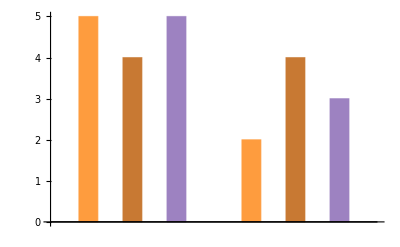

```mathematica
BarChart[WLexerciseBin["Entries"]]
```